# PPPC Plotter 06

Flip Tanedo
23 February 2013

If you use this, please cite Rajaraman, Smolinsky, Tanedo (2015).

Using the results of PPPCMachineRunner_03.nb, which in turn depended on PPPCMachineReader_01.nb and PPPCMachine....nb, written by FT. All of this is based on the PPPC4DMID package by Marco Cirelli et al. (1012.4515):

http://www.marcocirelli.net/PPPC4DMID.html

Updates from previous versions:
Streamlined

```mathematica
(*ClearAll["Global`*"]*) (* Not this time. Don't want to clear previous data. *)
```

## Run This Block To Initialize

## Source Files

Paths for files that contain processed data.

```mathematica
ProcessedDataDirectory="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData/";
```

## DC’s SaveIt and ReadIt functions

http://www.terpconnect.umd.edu/%7Edcurtin1/mathematica.html
See also DumpSave, http://mathematica.stackexchange.com/questions/1959/how-do-i-save-a-variable-or-function-definition-to-a-file
... but DC says this carries the risk of overwriting things because Mathematica saves the initial variable assignment, not just the object itself.

Functions courtesy of David Curtin.

```mathematica
(* to avoid memory bloat *)
ClearMemory:=Module[{},Unprotect[In,Out];
Clear[In,Out];
Protect[In,Out];
ClearSystemCache[];];

SaveIt[filename_,expr_]:=Module[{output},
output=Export[filename<>".dat",ToString[expr//InputForm],"String"];
ClearMemory;
output];
SaveIt[varnamestring_]:=Module[{output},output=Export[varnamestring<>".dat",ToString[ToExpression[varnamestring]//InputForm],"String"];
ClearMemory;
output];

ReadIt[filename_]:=Module[{output},output=ToExpression[Import[StringReplace[filename,".dat"->""]<>".dat","String"]];
ClearMemory;
output];
```

## J factors (run this)

PPPCMachine_CombinedPipeline gives some tools for generating and analyzing profiles for on-shell mediators. (See PPPC Machine Runner for examples for the run/driver file I used.) It does not specify a particular J factor, this depends on the type of analysis we’re using. These default are for the FERMI galactic center diffuse gamma ray search, 2014/2015. 

From JFactorsGC.nb (Flip Tanedo, 6 Feb 2015) which explicitly calcualtes the volume integral for a given set of parametrs.

### Unit Conversions and Parameters

All units should go to GeV and cm. Angles are measured given in degrees.

```mathematica
kpc=3.09 10^21 (*cm*);
rs=20 kpc; (* scale factor *)
ro=8.5 kpc; (* distance to galactic center *)
ρo=0.4; (* local DM density in GeV/cm^3 *)
rad = π/180;
```

### Generalized NFW

This is the generalized NFW profile written in coordinates where the origin is the galactic cetner.

```mathematica
ρnfw[r_,ρ0_,rs_,γ_]:=ρ0/((r/rs)^γ(1+r/rs)^(3-γ))
```

ρ0 is an overall constant that is chosen to enforce ρ(r=ro) = ρo. ((Note that the o≠0 ... one is the distance from Earth to the galactic center (o) and one is “naught.”))

```mathematica
rho0[γ_]:=(ro/rs)^γ(1+ro/rs)^(3-γ)ρo
```

### Pull out overall prefactor

Define NFW density as ρ/ρ0. We can multiply in factors of ρ0 as needed afterwards.

```mathematica
nnfw[r_,γ_]:=1/((r/rs)^γ(1+r/rs)^(3-γ))
```

### Shift to Galactic Coordinates

We want the NFW profile in Galactic coordinates, (d, b, l). See for example section 5.1 of 1012.4515 (PPPC). In Galactic coordinates, Earth is at the origin and the Galactic Center is located at x = ro. One then uses spherical coordinates where l is the azimuthal angle (ϕ) and b is the angle from the Galactic plane (xy plane). In other words, b is the complement of the usual polar angle with respect to z.

```mathematica
nnfw[√((x-ro)^2+y^2+z^2)/.{x->d Cos[el]Cos[b],y->d Sin[el]Cos[b],z->d Sin[b] },γ]//FullSimplify
```

((6.8985×10^44+d^2-5.253×10^22 d Cos[b] Cos[el])^(-γ/2) (6.18×10^22+1. √(6.8985×10^44+d^2-5.253×10^22 d Cos[b] Cos[el]))^γ)/(1.+1.61812×10^-23 √(6.8985×10^44+d^2-5.253×10^22 d Cos[b] Cos[el]))^3

Just copying and pasting that output into a new function that gives the NFW density in Galactic coordinates.

```mathematica
nGC[d_,b_,el_,γ_]:=((6.89850225*^44+d^2-5.253*^22 d Cos[b] Cos[el])^(-γ/2) (6.18*^22+1. √(6.89850225*^44+d^2-5.253*^22 d Cos[b] Cos[el]))^γ)/(1.+1.6181229773462784*^-23 √(6.89850225*^44+d^2-5.253*^22 d Cos[b] Cos[el]))^3
```

### Discussion

The J factor is an overlap integral

J=∫ρ_NFW^2  1/(4π r^2) ⅆV = ρ_0^2∫n_NFW^2 1/(4π r^2)ⅆV

Where the volume is the solid angle of the region of interest integrated over lines of sight from Earth.  The factor of 1/(4π r^2) accounts for the average over the annihilation product directions (i.e. the fraction of which that arrive at Earth). We typically pull the factor of 4π out of the definition of J. 

The volume element in Galactic coordinates is:

r^2 Cos[b]

### Integration parameters

We’ll integrate over a quadrant and then multiply by four, i.e. b, l >0. 

Choose 15 x 15 degree ‘box.’

```mathematica
bmin=0 rad;
bmax=7.5 rad;
lmin=0 rad;
lmax=7.5 rad;
```

### Integral as a function of γ

Note that this is not integrated over angles.

```mathematica
Jfac[γ_]:=4 NIntegrate[nGC[d,b,el,γ]^2 (d^2 Cos[b])/d^2,{b,bmin,bmax},{el,lmin,lmax},{d,0,∞}] rho0[γ]^2
```

```mathematica
JFermi=Jfac[1.2]//Quiet
```

1.08012×10^23

### Average J-factor: divide by solid angle

Jbar is given in GeV^2/cm^5/sr

```mathematica
SolidAngle[b_,ell_]:=4Integrate[Cos[bb],{bb,0,b},{l,0,ell}]
```

```mathematica
Jbar=Jfac[1.2]/SolidAngle[bmax,lmax]//Quiet
```

1.58044×10^24

## J-factor results (use these)

### Thermal Cross Section

```mathematica
σvth=2 (*Dirac*) 2.2 10^-26 (*cm^3/s*);
```

### Conversion

prefactor = 1/(4π η)J (<σv>)/m_χ^2

```mathematica
JtoSig=(1/(4π 4)JFermi σvth )^-1
```

10576.5

So the formula to interpret normalizations: 
1. multiply by JtoSig
2. multiply by mχ^2

## Functions for Grabbing Data

### Minimum Envelope

```mathematica
MinAGrid[datum_]:=Join[datum[[3]],{datum[[6]]}]
```

### Annihilation cross section in units of the thermal cross section

```mathematica
ARange[datum_]:=Join[datum[[3]],datum[[5]]]
```

#### Factor from Thermal

Distance from the thermal cross section

```mathematica
(* convert infinities in Max/Min into zeros... I may change them later *)
ProcessARange[point_]:=
If[point[[3]]==∞,
{point[[1]],point[[2]],0,0},
{point[[1]],point[[2]],point[[3]],point[[4]]}]

(* convert normalization into multiplcative factor from (Dirac) thermal Xsec *)
ConvertToThermalUnits[point_]:=Module[{temp},
temp = point;
temp[[3]] = point[[1]]^2 JtoSig point[[3]];
temp[[4]] = point[[1]]^2 JtoSig point[[4]];
temp
]

(* multiplicative distance from thermal *)
FactorFromThermal[point_]:=Module[{},
Which[point[[4]]<1, point[[4]],
point[[3]]<1&&point[[4]]≥1, 0,
point[[3]] ≥1, point[[3]]
]
]

ConvertToFactorFromThermal[point_]:={point[[1]],point[[2]],FactorFromThermal[point]}
```

### Masking

The problem with the above code is that I set “infinite” normalizations (i.e. there is no normalization that fits for this shape). In the above code I set infinity to zero norm, which makes for nice color gradients. If you change to, say, 100 then the colors get ugly (even for the well behaved regions) because of the way the Hue function works. I don’t know. This is a semi-black box for me.

My solution is to process these separately. Use this code to generate an interpolating function which can then be converted into a mask to remove the offending points.

```mathematica
(* convert infinities in Max/Min into zeros... I may change them later *)
ProcessARange2[point_]:=
If[point[[3]]==∞,
{point[[1]],point[[2]],"INF","INF"},
{point[[1]],point[[2]],point[[3]],point[[4]]}]

(* convert normalization into multiplcative factor from (Dirac) thermal Xsec *)
ConvertToThermalUnits2[point_]:=Module[{temp},
temp = point;
temp[[3]] =
If[point[[3]]=="INF",
100 (* arbitrary stupidly large number *),
 point[[1]]^2 JtoSig point[[3]]];
temp[[4]] =
If[point[[4]]=="INF",
100,
point[[1]]^2 JtoSig point[[4]]
] ;
temp
]
```

### Misc functions

http://mathematica.stackexchange.com/questions/3726/listloglinearplot-logarithmic-axis-tickmarks

```mathematica
exponentForm[num_?NumericQ]:=ToString@NumberForm[N@#1,ExponentFunction->(#&),NumberFormat->(#3&)]&@num
```

## Analyses

See file PPPCMachineRunner_01a.nb for top-charm contact interaction. 
Running this block outputs files into: /Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/

## Vbb

### Grab all relevant data files

```mathematica
vbb01=ReadIt[ProcessedDataDirectory<>"Vbb01"];
vbb02=ReadIt[ProcessedDataDirectory<>"Vbb02"];
vbb03=ReadIt[ProcessedDataDirectory<>"Vbb03"];
vbb04=ReadIt[ProcessedDataDirectory<>"Vbb04"];
vbb05=ReadIt[ProcessedDataDirectory<>"Vbb05"];
vbig01=ReadIt[ProcessedDataDirectory<>"Vb_big_01"];
vbig02=ReadIt[ProcessedDataDirectory<>"Vb_big_02"];
vbig03=ReadIt[ProcessedDataDirectory<>"Vb_big_03"];

vbb=Join[vbb01,vbb02,vbb03,vbb04,vbb05,vbig01,vbig02,vbig03];
Length[vbb]
```

7437

### A nicer way to get files

```mathematica
SetDirectory["/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData/"]
vbbs=FileNames["Vb*"];
vbbnames=StringSplit[#,"."][[1]]&/@vbbs
vbb=Join[Flatten[ReadIt/@vbbnames,1]];
Length[vbb]
```

/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData

{Vbb01,Vbb02,Vbb03,Vbb04,Vbb05,Vb_big_01,Vb_big_02,Vb_big_03}

7437

### Minimum A, constructing data and cleaning

7390

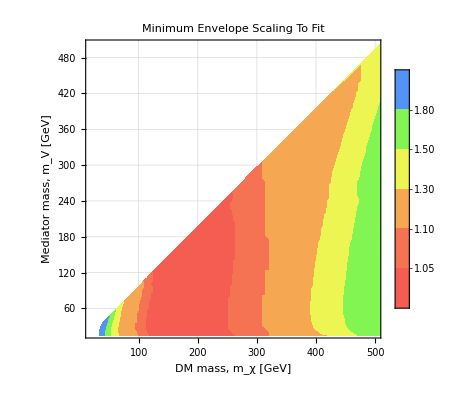

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vbbA.png

```mathematica
minAvbb=MinAGrid/@vbb;

(* Remove any data that with A=10, these are problematic points *)
minAvbbClean=Select[minAvbb,#[[3]]!=10&];
Length[minAvbbClean]

(* Make the plot, may need to tweak options *)
ListContourPlot[minAvbbClean,InterpolationOrder->10,
Contours->{1,1.05,1.1,1.3,1.5,1.8},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},y<x],
ColorFunction->(Hue[.6# ,2/3  ,0.75+0.211]&),
(*PlotLegends->Automatic,*)
(*PlotLegends->Placed[{1,1.05,1.1,1.3,1.5,1.8},{.15,.6}],*)
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendMargins->{1,1.05,1.1,1.3,1.5,1.8}]
,{.125,.55}],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_V [GeV]"},
PlotLabel->"Minimum Envelope Scaling To Fit",
FrameStyle->Thickness[.0031],
PlotRange->{{20,500},{20,500},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["V→bb",15,Darker[Black]],0Degree],ImageScaled@{.24,.88}]*)
Text[Style["χχ̄→VV (V→bb̄)",15,Black],ImageScaled@{.32,.88}]
}
]

(* Output the plot *)
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vbbA.png",%]
```

### Factor from Thermal

7437

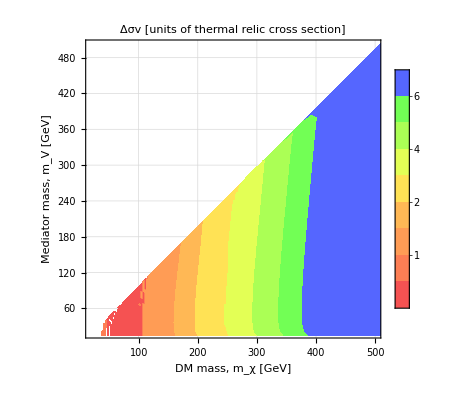

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vbbxec.png

```mathematica
factorfromthermalvbb=ConvertToFactorFromThermal/@ConvertToThermalUnits/@ProcessARange/@ARange/@vbb;
Length[%]

(* Interpolating function for masking purposes *)
interpolVbb=Interpolation[ConvertToFactorFromThermal/@ConvertToThermalUnits2/@ProcessARange2/@ARange/@vbb]//Quiet;

ListContourPlot[factorfromthermalvbb,InterpolationOrder->10,
(*Contours->10,*)
Contours->{.5,1,1.5,2,3,4,5,6},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},
y<x&&interpolVbb[x,y]<50],
(*ColorFunction->(Hue[.7# ,1-.8#  ,.9-.3# ]&),*)
ColorFunction->(Hue[.65# ,2/3  ,0.96+.5#]&),
(*PlotLegends->Automatic,*)
PlotLegends->Placed[{.5,1,1.5,2,3,4,5,6},{.1,.5}],
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_V [GeV]"},
(*PlotLabel->"σv [units of thermal relic cross section]",*)
PlotLabel->"Δσv [units of thermal relic cross section]",
FrameStyle->Thickness[.003],
PlotRange->{{20,500},{20,500},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["V→bb, a=2",15,Darker[Black]],0Degree],ImageScaled@{.26,.88}]*)
Text[Style["χχ̄→VV (V→bb̄), a=2",15,Black],ImageScaled@{.35,.88}]
}
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vbbxec.png",%]
```

## Vqq

### Grab all relevant data files

```mathematica
vbb01=ReadIt[ProcessedDataDirectory<>"Vbb01"];
vbb02=ReadIt[ProcessedDataDirectory<>"Vbb02"];
vbb03=ReadIt[ProcessedDataDirectory<>"Vbb03"];
vbb04=ReadIt[ProcessedDataDirectory<>"Vbb04"];
vbb05=ReadIt[ProcessedDataDirectory<>"Vbb05"];
vbig01=ReadIt[ProcessedDataDirectory<>"Vb_big_01"];
vbig02=ReadIt[ProcessedDataDirectory<>"Vb_big_02"];
vbig03=ReadIt[ProcessedDataDirectory<>"Vb_big_03"];

vbb=Join[vbb01,vbb02,vbb03,vbb04,vbb05,vbig01,vbig02,vbig03];
Length[vbb]
```

7437

### A nicer way to get files

```mathematica
SetDirectory["/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData/"]
vqqs=FileNames["Vq*"];
vqqnames=StringSplit[#,"."][[1]]&/@vqqs
vqq=Join[Flatten[ReadIt/@vqqnames,1]];
Length[vqq]
```

/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData

{Vq_big_01,Vq_big_02,Vq_big_03,Vqq01,Vqq02,Vqq03,Vqq04,Vqq05}

7437

### Minimum A, constructing data and cleaning

7391

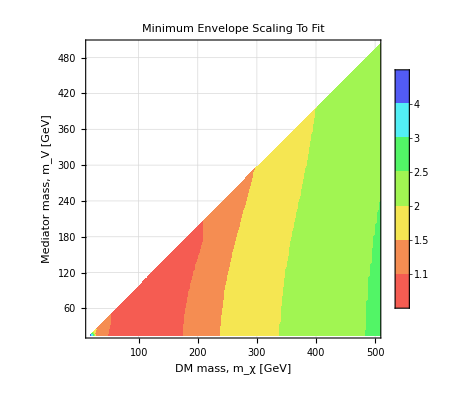

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vqqA.png

```mathematica
minAvqq=MinAGrid/@vqq;

(* Remove any data that with A=10, these are problematic points *)
minAvqqClean=Select[minAvqq,#[[3]]!=10&];
Length[minAvqqClean]

(* Make the plot, may need to tweak options *)
ListContourPlot[minAvqqClean,InterpolationOrder->10,
(*Contours->{1,1.05,1.1,1.3,1.5,1.8},*)
Contours->{1,1.1,1.5,2,2.5,3,4,4.5,5},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},y<x],
ColorFunction->(Hue[.7# ,2/3  ,0.75+0.211]&),
(*PlotLegends->Automatic,*)
(*PlotLegends->Placed[{1,1.05,1.1,1.3,1.5,1.8},{.15,.6}],*)
(*PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendMargins->{1,1.05,1.1,1.3,1.5,1.8}]
,{.125,.55}],*)
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200]
,{.125,.55}],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_V [GeV]"},
PlotLabel->"Minimum Envelope Scaling To Fit",
FrameStyle->Thickness[.0031],
PlotRange->{{20,500},{20,500},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["V→qq",15,Darker[Black]],0Degree],ImageScaled@{.23,.88}]*)
Text[Style["χχ̄→VV (V→qq̄)",15,Black],ImageScaled@{.32,.88}]
}
]

(* Output the plot *)
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vqqA.png",%]
```

### Factor from Thermal

7437

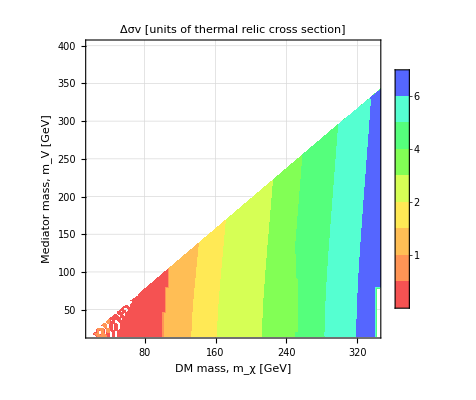

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vqqxec.png

```mathematica
factorfromthermalvqq=ConvertToFactorFromThermal/@ConvertToThermalUnits/@ProcessARange/@ARange/@vqq;
Length[%]

(* Interpolating function for masking purposes *)
interpolVqq=Interpolation[ConvertToFactorFromThermal/@ConvertToThermalUnits2/@ProcessARange2/@ARange/@vqq]//Quiet;

ListContourPlot[factorfromthermalvqq,InterpolationOrder->10,
(*Contours->10,*)
Contours->{.5,1,1.5,2,3,4,5,6},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},
y<x&&interpolVqq[x,y]<50],
(*ColorFunction->(Hue[.7# ,1-.8#  ,.9-.3# ]&),*)
ColorFunction->(Hue[.65# ,2/3  ,0.96+.5#]&),
(*PlotLegends->Automatic,*)
PlotLegends->Placed[{.5,1,1.5,2,3,4,5,6},{.1,.5}],
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_V [GeV]"},
PlotLabel->"Δσv [units of thermal relic cross section]",
FrameStyle->Thickness[.003],
(*PlotRange->{{20,500},{20,500},Automatic},*)
PlotRange->{{20,340},{20,400},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["V→qq, a=2",15,Darker[Black]],0Degree],ImageScaled@{.25,.88}]*)
Text[Style["χχ̄→VV (V→qq̄), a=2",15,Black],ImageScaled@{.35,.88}]
}
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vqqxec.png",%]
```

## ϕbb

### A nicer way to get files

```mathematica
SetDirectory["/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData/"]
phibs=FileNames["phib*"];
phibnames=StringSplit[#,"."][[1]]&/@phibs
phi3b=Join[Flatten[ReadIt/@phibnames,1]];
Length[phi3b]
```

/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData

{phib_01,phib_02,phib_03,phib_04,phibbig_01,phibbig_02}

6280

### Minimum A, constructing data and cleaning

6236

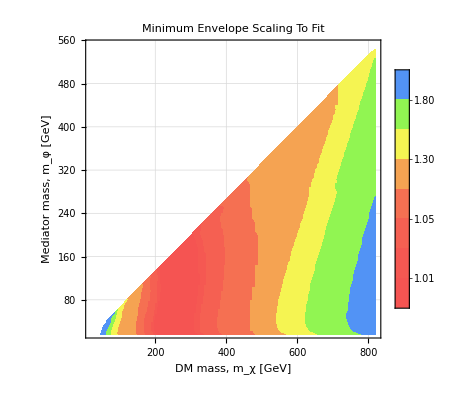

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pbbA.png

```mathematica
minApbb=MinAGrid/@phi3b;

(* Remove any data that with A=10, these are problematic points *)
minApbbClean=Select[minApbb,#[[3]]!=10&];
Length[minApbbClean]

(* Make the plot, may need to tweak options *)
ListContourPlot[minApbbClean,InterpolationOrder->10,
(*Contours->{1,1.05,1.1,1.3,1.5,1.8},*)
Contours->{1,1.01,1.02,1.05,1.1,1.3,1.5,1.8},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},y<x],
ColorFunction->(Hue[.6# ,2/3  ,0.75+0.211]&),
(*PlotLegends->Automatic,*)
(*PlotLegends->Placed[{1,1.05,1.1,1.3,1.5,1.8},{.15,.6}],*)
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,LegendMargins->{1,1.05,1.1,1.3,1.5,1.8}]
,{.125,.55}],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_φ [GeV]"},
PlotLabel->"Minimum Envelope Scaling To Fit",
FrameStyle->Thickness[.0031],
PlotRange->{{20,819},{20,550},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["φ→bb",15,Darker[Black]],0Degree],ImageScaled@{.255,.88}]*)
Text[Style["χχ̄→3φ (φ→bb̄)",15,Black],ImageScaled@{.33,.89}]
}
]

(* Output the plot *)
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pbbA.png",%]
```

### Factor from Thermal

6280

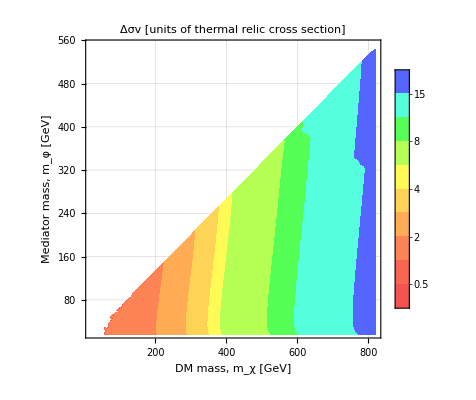

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pbbxec.png

```mathematica
factorfromthermalpbb=ConvertToFactorFromThermal/@ConvertToThermalUnits/@ProcessARange/@ARange/@phi3b;
Length[%]

(* Interpolating function for masking purposes *)
interpolpbb=Interpolation[ConvertToFactorFromThermal/@ConvertToThermalUnits2/@ProcessARange2/@ARange/@phi3b]//Quiet;

ListContourPlot[factorfromthermalpbb,InterpolationOrder->10,
(*Contours->10,*)
Contours->{.5,1,2,3,4,5,8,10,15},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},
y<x&&interpolpbb[x,y]<50],
(*ColorFunction->(Hue[.7# ,1-.8#  ,.9-.3# ]&),*)
ColorFunction->(Hue[.65# ,2/3  ,0.96+.5#]&),
(*PlotLegends->Automatic,*)
PlotLegends->Placed[{.5,1,2,3,4,5,8,10,15},{.1,.5}],
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_φ [GeV]"},
PlotLabel->"Δσv [units of thermal relic cross section]",
FrameStyle->Thickness[.003],
PlotRange->{{20,819},{20,550},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["φ→bb, a=2",15,Darker[Black]],0Degree],ImageScaled@{.26,.88}]*)
Text[Style["χχ̄→3φ (φ→bb̄), a=2",15,Black],ImageScaled@{.35,.89}]
}
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pbbxec.png",%]
```

## ϕqq

### A nicer way to get files

```mathematica
SetDirectory["/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData/"]
phiqs=FileNames["phiq*"];
phiqnames=StringSplit[#,"."][[1]]&/@phiqs
phi3q=Join[Flatten[ReadIt/@phiqnames,1]];
Length[phi3q]
```

/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData

{phiq_01,phiq_02,phiq_03,phiq_04,phiqbig_01,phiqbig_02}

6280

### Minimum A, constructing data and cleaning

6240

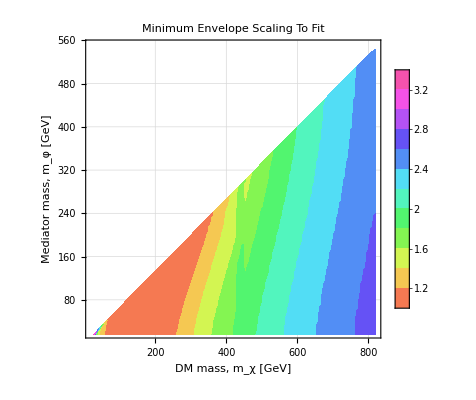

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pqqA.png

```mathematica
minApqq=MinAGrid/@phi3q;

(* Remove any data that with A=10, these are problematic points *)
minApqqClean=Select[minApqq,#[[3]]!=10&];
Length[minApqqClean]

(* Make the plot, may need to tweak options *)
ListContourPlot[minApqqClean,InterpolationOrder->10,
(*Contours->{1,1.05,1.1,1.3,1.5,1.8},*)
Contours->Range[1,3.5,.2],
ContourStyle->None,
RegionFunction-> Function[{x,y,z},y<x],
ColorFunction->(Hue[.9# ,2/3  ,0.75+0.211]&),
(*PlotLegends->Automatic,*)
(*PlotLegends->Placed[{1,1.05,1.1,1.3,1.5,1.8},{.15,.6}],*)
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,(*LegendMargins->{1,1.05,1.5,2,4,5,6,7,8,9,10}*)
LegendMargins->Range[1,3,.2]
]
,{.125,.55}],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_φ [GeV]"},
PlotLabel->"Minimum Envelope Scaling To Fit",
FrameStyle->Thickness[.0031],
PlotRange->{{20,819},{20,550},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["φ→qq",15,Darker[Black]],0Degree],ImageScaled@{.26,.88}]*)
Text[Style["χχ̄→3φ (φ→qq̄)",15,Black],ImageScaled@{.32,.89}]
}
]

(* Output the plot *)
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pqqA.png",%]
```

### Factor from Thermal

6280

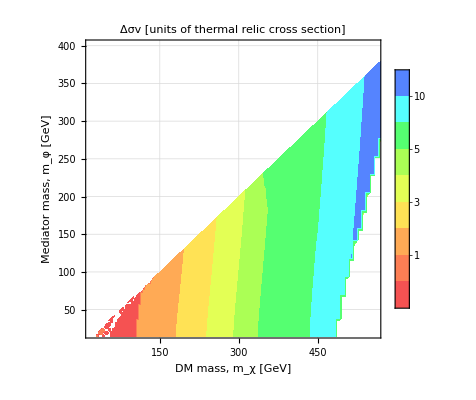

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pqqxec.png

```mathematica
factorfromthermalpqq=ConvertToFactorFromThermal/@ConvertToThermalUnits/@ProcessARange/@ARange/@phi3q;
Length[%]

(* Interpolating function for masking purposes *)
interpolpqq=Interpolation[ConvertToFactorFromThermal/@ConvertToThermalUnits2/@ProcessARange2/@ARange/@phi3q]//Quiet;

ListContourPlot[factorfromthermalpqq,InterpolationOrder->10,
(*Contours->10,*)
Contours->{.5,1,2,3,4,5,8,10,15},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},
y<x&&interpolpqq[x,y]<50],
(*ColorFunction->(Hue[.7# ,1-.8#  ,.9-.3# ]&),*)
ColorFunction->(Hue[.65# ,2/3  ,0.96+.5#]&),
(*PlotLegends->Automatic,*)
PlotLegends->Placed[{.5,1,2,3,4,5,8,10,15},{.1,.5}],
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_φ [GeV]"},
PlotLabel->"Δσv [units of thermal relic cross section]",
FrameStyle->Thickness[.003],
PlotRange->{{20,559},{20,400},Automatic},
PlotRangeClipping->True,
Epilog->{
(*Text[Rotate[Style["φ→qq, a=2",15,Darker[Black]],0Degree],ImageScaled@{.27,.88}]*)
Text[Style["χχ̄→3φ (φ→qq̄), a=2",15,Black],ImageScaled@{.35,.89}]
}
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/pqqxec.png",%]
```

## top-charm Modes

Maybe ignore these... they don’t really get boosted anyway.

### Nicer way to get the files

```mathematica
SetDirectory["/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData/"]
```

/Users/fliptanedo/Documents/Work/PPPCMachineRunner/ProcessedData

```mathematica
phitc=FileNames["phitc*"]
Vtc=FileNames["Vtc*"]
```

{phitc_01.dat,phitc_big_01.dat}

{Vtc_01.dat,Vtc_big_01.dat}

```mathematica
phitcs=StringSplit[#,"."][[1]]&/@phitc
Vtcs=StringSplit[#,"."][[1]]&/@Vtc
```

{phitc_01,phitc_big_01}

{Vtc_01,Vtc_big_01}

```mathematica
phi3tc=Join[Flatten[ReadIt/@phitcs,1]];
V2tc=Join[Flatten[ReadIt/@Vtcs,1]];
Length[phi3tc]
Length[V2tc]
```

Range::argb: Range called with 0 arguments; between 1 and 3 arguments are expected.

General::stop: Further output of Range :: argb will be suppressed during this calculation.

1996

3984

There seems to be some problem with the some elements of phi3tc.

```mathematica
phi3tcGood=phi3tc[[2;;]];
```

```mathematica
Length[phi3tcGood]
```

1995

```mathematica
phi3tcBetter=Select[phi3tc,NumericQ[#[[5]][[1]]]&&NumericQ[#[[5]][[1]]]&];
```

```mathematica
Length[phi3tcBetter]
```

588

#### Vtc: Min A

3984

3984

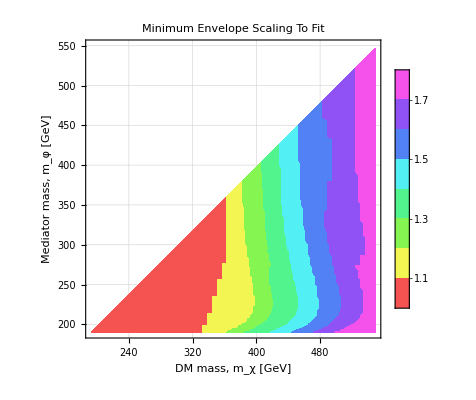

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vtcA.png

```mathematica
minAVtc=MinAGrid/@V2tc;
Length[minAVtc]

minAVtcClean=Select[minAVtc,#[[3]]!=10&];
Length[minAVtcClean]

ListContourPlot[minAVtcClean,InterpolationOrder->10,
(*Contours->{1,1.01,1.02,1.05,1.1,1.3,1.5,1.8},*)
(*Contours->Range[1,3.5,.2],*)
ContourStyle->None,
RegionFunction-> Function[{x,y,z},y<x],
ColorFunction->(Hue[.9# ,2/3  ,0.75+0.211]&),
(*PlotLegends->Automatic,*)
(*PlotLegends->Placed[{1,1.05,1.1,1.3,1.5,1.8},{.15,.6}],*)
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,(*LegendMargins->{1,1.05,1.5,2,4,5,6,7,8,9,10}*)
LegendMargins->Range[1,3,.2]
]
,{.125,.55}],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_φ [GeV]"},
PlotLabel->"Minimum Envelope Scaling To Fit",
FrameStyle->Thickness[.0031],
PlotRange->{{193,549},{190,550},Automatic},
PlotRangeClipping->True,
Epilog->{
Text[Rotate[Style["V→tc",15,Darker[Black]],0Degree],ImageScaled@{.25,.88}]
}
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vtcA.png",%]
```

1995

588

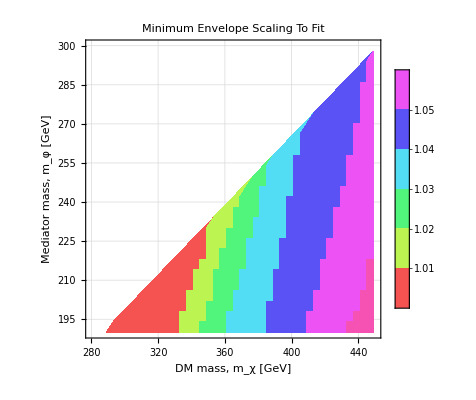

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/ptcA.png

```mathematica
minA3tc=MinAGrid/@phi3tcGood;
Length[minA3tc]

minA3tcClean=Select[minA3tc,#[[3]]!=10&];
Length[minA3tcClean]

ListContourPlot[minA3tcClean,InterpolationOrder->10,
(*Contours->{1,1.01,1.02,1.05,1.1,1.3,1.5,1.8},*)
(*Contours->Range[1,3.5,.2],*)
ContourStyle->None,
RegionFunction-> Function[{x,y,z},y<x],
ColorFunction->(Hue[.9# ,2/3  ,0.75+0.211]&),
(*PlotLegends->Automatic,*)
(*PlotLegends->Placed[{1,1.05,1.1,1.3,1.5,1.8},{.15,.6}],*)
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,(*LegendMargins->{1,1.05,1.5,2,4,5,6,7,8,9,10}*)
LegendMargins->Range[1,3,.2]
]
,{.125,.55}],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_φ [GeV]"},
PlotLabel->"Minimum Envelope Scaling To Fit",
FrameStyle->Thickness[.0031],
PlotRange->{{280,450},{190,300},Automatic},
PlotRangeClipping->True,
Epilog->{
Text[Rotate[Style["φ→tc",15,Darker[Black]],0Degree],ImageScaled@{.25,.88}]
}
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/ptcA.png",%]
```

BUT NOTE: not a big change in the min normalization, but the specturm doesn’t fit beyond this small triangle

#### Extra

```mathematica
minA3tc=MinAGrid/@phi3tcBetter;
Length[minA3tc]

minA3tcClean=Select[minA3tc,#[[3]]!=10&];
Length[minA3tcClean]

ListContourPlot[minA3tcClean,InterpolationOrder->10,
(*Contours->{1,1.01,1.02,1.05,1.1,1.3,1.5,1.8},*)
(*Contours->Range[1,3.5,.2],*)
ContourStyle->None,
RegionFunction-> Function[{x,y,z},y<x],
ColorFunction->(Hue[.9# ,2/3  ,0.75+0.211]&),
(*PlotLegends->Automatic,*)
(*PlotLegends->Placed[{1,1.05,1.1,1.3,1.5,1.8},{.15,.6}],*)
PlotLegends->Placed[BarLegend[Automatic,LegendMarkerSize->200,(*LegendMargins->{1,1.05,1.5,2,4,5,6,7,8,9,10}*)
LegendMargins->Range[1,3,.2]
]
,{.125,.55}],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_φ [GeV]"},
PlotLabel->"Minimum Envelope Scaling To Fit",
FrameStyle->Thickness[.0031],
PlotRange->{{280,450},{190,300},Automatic},
PlotRangeClipping->True,
Epilog->{
Text[Rotate[Style["φ→tc",13,Darker[Black]],0Degree],ImageScaled@{.25,.88}]
}
]
```

588

588

-Graphics-

#### Vtc: Factor from Thermal

```mathematica
factorfromthermalVtc=ConvertToFactorFromThermal/@ConvertToThermalUnits/@ProcessARange/@ARange/@V2tc;
Length[%]
```

3984

```mathematica
FactorInteger[3984]
```

{{2,4},{3,1},{83,1}}

```mathematica
interpolVtc=Interpolation[ConvertToFactorFromThermal/@ConvertToThermalUnits2/@ProcessARange2/@ARange/@V2tc]//Quiet;
```

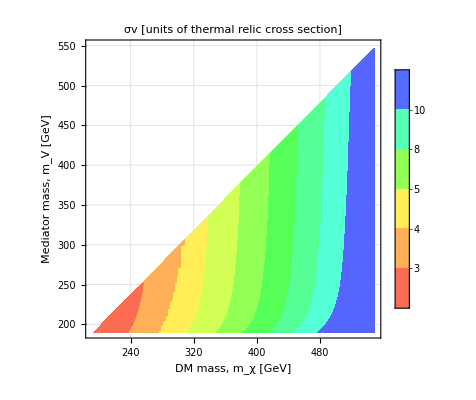

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vtcxec.png

```mathematica
ListContourPlot[factorfromthermalVtc,InterpolationOrder->10,
(*Contours->10,*)
Contours->{.5,1,2,3,4,5,6,7,8,9,10},
ContourStyle->None,
RegionFunction-> Function[{x,y,z},
y<x&&interpolVtc[x,y]<50],
(*ColorFunction->(Hue[.7# ,1-.8#  ,.9-.3# ]&),*)
ColorFunction->(Hue[.65# ,2/3  ,0.96+.5#]&),
(*ColorFunction->(Hue[.75# ,.8  ,0.96+.5#]&),*)
(*PlotLegends->Automatic,*)
PlotLegends->Placed[{.5,1,2,3,4,5,8,10,15},{.1,.5}],
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_V [GeV]"},
PlotLabel->"σv [units of thermal relic cross section]",
FrameStyle->Thickness[.003],
PlotRange->{{190,550},{190,550},Automatic},
PlotRangeClipping->True,
Epilog->{
Text[Rotate[Style["V→tc, a=2",15 ,Darker[Black]],0Degree],ImageScaled@{.25,.88}]
}
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/vtcxec.png",%]
```

#### phitc: Factor from Thermal

```mathematica
factorfromthermalptc=ConvertToFactorFromThermal/@ConvertToThermalUnits/@ProcessARange/@ARange/@phi3tcBetter;
Length[%]
```

588

```mathematica
interpolptc=Interpolation[ConvertToFactorFromThermal/@ConvertToThermalUnits2/@ProcessARange2/@ARange/@phi3tcBetter]//Quiet;
```

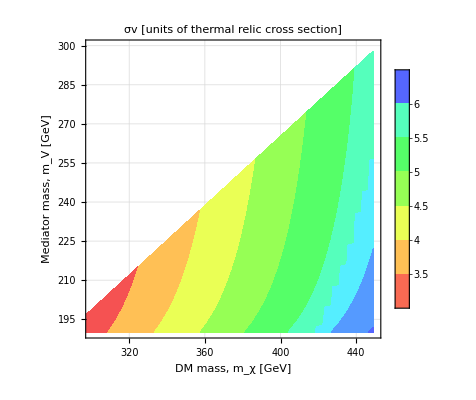

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/ptcxec.png

```mathematica
ListContourPlot[factorfromthermalptc,InterpolationOrder->10,
(*Contours->10,*)
(*Contours->{.5,1,2,3,4,5,8,10,15},*)
ContourStyle->None,
RegionFunction-> Function[{x,y,z},
y<x&&interpolptc[x,y]<50],
(*ColorFunction->(Hue[.7# ,1-.8#  ,.9-.3# ]&),*)
ColorFunction->(Hue[.65# ,2/3  ,0.96+.5#]&),
(*ColorFunction->(Hue[.75# ,.8  ,0.96+.5#]&),*)
(*PlotLegends->Automatic,*)
PlotLegends->Placed[Range[1,6,.5],{.1,.6}],
BaseStyle->{FontFamily->"Helvetica",FontSize->13},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"DM mass, m_χ [GeV]","Mediator mass, m_V [GeV]"},
PlotLabel->"σv [units of thermal relic cross section]",
FrameStyle->Thickness[.003],
PlotRange->{{300,450},{190,300},Automatic},
PlotRangeClipping->True,
Epilog->{
Text[Rotate[Style["φ→tc, a=2",15,Darker[Black]],0Degree],ImageScaled@{.26,.88}]
}
]
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/ptcxec.png",%]
```

# Additional Plots

USES: PPPCMachine, PPPCMachineRunner_01a, MachineReader_03

## Background

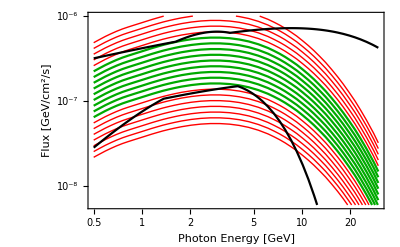

```mathematica
SuperPlot[p2gam["b",60,#]&,
RangeOfNorms[p2gam["b",60,#]&,MinEnv,MaxEnv,4,1,20],
MinEnv,MaxEnv,2,20,.5,30]
```

### Super Plot Code

Need to do things manually, can’t just super plot it. Here’s the superplot code for copying

```mathematica
SuperPlot[func_,norms_,MinEnv_,MaxEnv_,A_,numchecks_,minE_,maxE_]:=Module[
{goodnorms,badnorms},
goodnorms=GoodNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];

LogLogPlot[
Evaluate[Join[
x^2 func[x]#&/@goodnorms,
x^2 func[x]#&/@badnorms,

{MinEnv[x]/A,A MaxEnv[x]}]],
{x,minE,maxE},
PlotStyle->Join[
(* Good Curves: *)
Table[{Darker[Green]},{i,Length[goodnorms]}],
(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small]},{i,Length[badnorms]}],
(* Min/Max curves: *)
{{Black},{Black}}],
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"}
(*PlotTheme->"Detailed"*)
]
]
```

### Thermal Cross Section

The conversion factor between the PPPC output dN/dE and the flux is

E^2 dΦ/dE=E^2 1/(4πη)(<σv>)/m_x^2(dN/dE)_PPPC

```mathematica
1/(4π 4)JFermi σvth  (* but also divide by mx^2 *)
```

0.0000945489

#### Check:

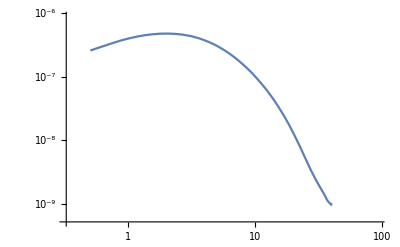

```mathematica
LogLogPlot[1/(4π 4)JFermi σvth 1/40^2 x^2 p2gam["b",40,x],{x,.5,60}]
```

## Making Plots

### Tests: 40, 50, 60

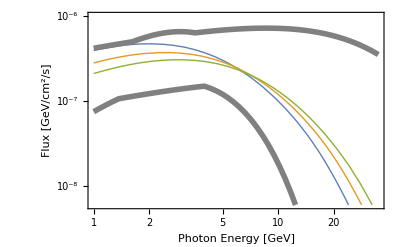

```mathematica
Module[{A,func,func1,func2,func3,mass,mass1,mass2,mass3,envstyle},
A=2;
mass1=40;
mass2=50;
mass3=60;
func1=p2gam["b",mass1,#]&;
func2=p2gam["b",mass2,#]&;
func3=p2gam["b",mass3,#]&;
envstyle={(*Thick,*)Thickness[.01],Gray};
LogLogPlot[
Evaluate[{
1/(4π 4)JFermi σvth/mass1^2 x^2 func1[x],
1/(4π 4)JFermi σvth/mass2^2 x^2 func2[x],
1/(4π 4)JFermi σvth/mass3^2 x^2 func3[x],

MinEnv[x]/A,A MaxEnv[x]}],
{x,minE,maxE},
(*PlotStyle->Join[
(* Good Curves: *)
Table[{Darker[Green]},{i,Length[goodnorms]}],
(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small]},{i,Length[badnorms]}],
(* Min/Max curves: *)
{{Black},{Black}}],*)
PlotStyle->{
{Thick},
{Thick},
{Thick},
envstyle,
envstyle
},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"}
(*PlotTheme->"Detailed"*)
]
]
```

### Looking for some points

#### VV to qq

```mathematica
(*VVqq100="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtoqq/VV_q_99_30.dat";*)
dirqq="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtoqq/VV_q";
fVVqq=GetFunc[dirqq,{81,21}];
```

#### pp to bb

```mathematica
dir3bb="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/3ptobb/3p_b";
f3pbb=GetFunc[dir3bb,{123,27}];
```

### Revised MinEnv

```mathematica
MinEnvR[x_]:=Piecewise[{{MinEnv[x],x<13}},10^-10]
```

### Some Fits: Multiplot

#### Just a Pretty Template

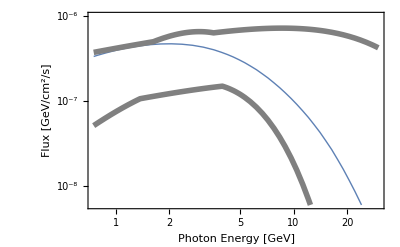

```mathematica
Module[{A,func,mass,envstyle,minE,maxE},
A=2;
mass=40;
func=p2gam["b",mass,#]&;
envstyle={(*Thick,*)Thickness[.01],Gray};
minE=.75;
maxE=30;
LogLogPlot[
Evaluate[{
1/(4π 4)JFermi σvth/mass1^2 x^2 func[x],
MinEnv[x]/A,A MaxEnv[x]}],
{x,minE,maxE},
PlotStyle->{
{Thick},
envstyle,
envstyle
},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"}
(*PlotTheme->"Detailed"*)
]
]
```

#### Multi Plot

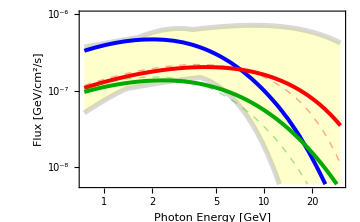

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/sampleplots.png

```mathematica
Module[{A,f1,f2,f3,f4,f5,m1,m2,m4,envstyle,minE,maxE},
A=2;
m1=40;
m2=81;
m4=123;
f1=p2gam["b",m1,#]&;
f2=fVVqq;
f3=p2gam["q",m2/2.,#]&;
f4=f3pbb;
f5=p2gam["b",m4/3.,#]&;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
LogLogPlot[
Evaluate[{
MinEnvR[x]/A,A MaxEnv[x],
1/(4π 4)JFermi σvth/m1^2 x^2 f1[x],
1/(4π 4)JFermi σvth/m2^2 x^2 f2[x],
1/(4π 4)JFermi (.5 (* for shape comparison *) σvth)/(m2/2)^2 x^2 f3[x],
1/(4π 4)JFermi σvth/m4^2 x^2 f4[x],
1/(4π 4)JFermi (.33 (* for shape comparison *) σvth)/(m4/3)^2 x^2 f5[x]
}],
{x,minE,maxE},
PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue},
{Thickness[.008],Red},
{Thick,Opacity[.35,Red],Dashed},
{Thickness[.008],Darker[Green]},
{Thick,Opacity[.35,Darker[Green]],Dashed}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"},
ImageSize->Medium, (* or Large*)
Epilog->{
Text[Rotate[Style["bb",14,Blue],0Degree],ImageScaled@{.35,.90}],
Text[Rotate[Style["m_χ=40 GeV",12,Blue],0Degree],ImageScaled@{.35,.75}],
Text[Rotate[Style["VV (V→qq)",14,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",12,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",14,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",12,Darker[Green]],0Degree],ImageScaled@{.5,.45}]
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]
]
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/sampleplots.png",%]
```

#### Make it bigger

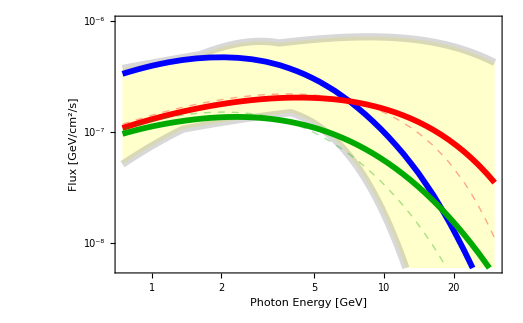

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/sampleplotsbig.png

```mathematica
Module[{A,f1,f2,f3,f4,f5,m1,m2,m4,envstyle,minE,maxE},
A=2;
m1=40;
m2=81;
m4=123;
f1=p2gam["b",m1,#]&;
f2=fVVqq;
f3=p2gam["q",m2/2.,#]&;
f4=f3pbb;
f5=p2gam["b",m4/3.,#]&;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
LogLogPlot[
Evaluate[{
MinEnvR[x]/A,A MaxEnv[x],
1/(4π 4)JFermi σvth/m1^2 x^2 f1[x],
1/(4π 4)JFermi σvth/m2^2 x^2 f2[x],
1/(4π 4)JFermi (.5 (* for shape comparison *) σvth)/(m2/2)^2 x^2 f3[x],
1/(4π 4)JFermi σvth/m4^2 x^2 f4[x],
1/(4π 4)JFermi (.33 (* for shape comparison *) σvth)/(m4/3)^2 x^2 f5[x]
}],
{x,minE,maxE},
PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue},
{Thickness[.008],Red},
{Thick,Opacity[.35,Red],Dashed},
{Thickness[.008],Darker[Green]},
{Thick,Opacity[.35,Darker[Green]],Dashed}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"},
ImageSize->Large, (* or Large*)
Epilog->{
Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.35,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.35,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}]
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]
]
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/sampleplotsbig.png",%]
```

#### Make it bigger: tweak axes

Using: http://mathematica.stackexchange.com/questions/3726/listloglinearplot-logarithmic-axis-tickmarks

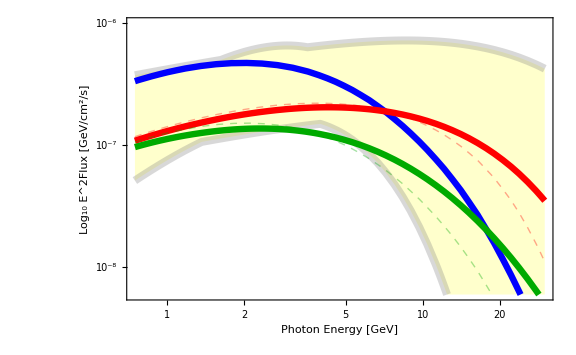

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/sampleplotsbig.png

```mathematica
Module[{A,f1,f2,f3,f4,f5,m1,m2,m4,envstyle,minE,maxE,expTicks},
A=2;
m1=40;
m2=81;
m4=123;
f1=p2gam["b",m1,#]&;
f2=fVVqq;
f3=p2gam["q",m2/2.,#]&;
f4=f3pbb;
f5=p2gam["b",m4/3.,#]&;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;

expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];

LogLogPlot[
Evaluate[{
MinEnvR[x]/A,A MaxEnv[x],
1/(4π 4)JFermi σvth/m1^2 x^2 f1[x],
1/(4π 4)JFermi σvth/m2^2 x^2 f2[x],
1/(4π 4)JFermi (.5 (* for shape comparison *) σvth)/(m2/2)^2 x^2 f3[x],
1/(4π 4)JFermi σvth/m4^2 x^2 f4[x],
1/(4π 4)JFermi (.33 (* for shape comparison *) σvth)/(m4/3)^2 x^2 f5[x]
}],
{x,minE,maxE},
PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue},
{Thickness[.008],Red},
{Thick,Opacity[.35,Red],Dashed},
{Thickness[.008],Darker[Green]},
{Thick,Opacity[.35,Darker[Green]],Dashed}
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large, (* or Large*)
FrameTicks->{Automatic,expTicks,{},{}},
Epilog->{
Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.27,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.27,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}],
Text[Style["a=2",19,Gray],ImageScaled@{.2,.23}]
}
(*PlotLegends->Placed[LineLegend[Range[1,6],LegendLayout->{"Row",2}],{.35,.25}]*)
(*PlotTheme->"Detailed"*)
]
]
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/sampleplotsbig.png",%]
```

### universal vs. light

#### Testing universal versus light quarks

```mathematica
dirqq="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtoqq/VV_q";
fVVqq=GetFunc[dirqq,{81,21}];
dirbb="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtobb/VV_b"
fVVbb=GetFunc[dirbb,{81,21}];
```

/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtobb/VV_b

#### Plotting the Test

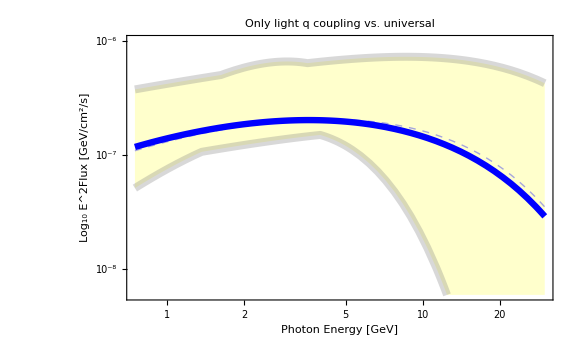

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/samplelightvsuniversal.png

```mathematica
Module[{A,f1,f2,m1,envstyle,minE,maxE,expTicks},
A=2;
m1=81;
f1[x_]:=4/5. fVVqq[x]+1/5. fVVbb[x];
f2=fVVqq;
envstyle={(*Thick,*)Thickness[.01],Opacity[.3,Gray]};
minE=.75;
maxE=30;
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];

LogLogPlot[
Evaluate[{
MinEnvR[x]/A,A MaxEnv[x],
1/(4π 4)JFermi σvth/m1^2 x^2 f1[x],
1/(4π 4)JFermi σvth/m1^2 x^2 f2[x],
}],
{x,minE,maxE},
PlotStyle->{
envstyle,
envstyle,
{Thickness[.008],Blue},
{Thick,Opacity[.35,Blue],Dashed},
},
Filling->{1->{2}},
FillingStyle->{Opacity[.2,Yellow]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
PlotLabel->"Only light q coupling vs. universal",
ImageSize->Large (* or Large*)
(*Epilog->{
Text[Rotate[Style["bb",19,Blue],0Degree],ImageScaled@{.35,.92}],
Text[Rotate[Style["m_χ=40 GeV",17,Blue],0Degree],ImageScaled@{.35,.78}],
Text[Rotate[Style["VV (V→qq)",19,Red],0Degree],ImageScaled@{.83,.84}],
Text[Rotate[Style["m_χ=81, m_V=21 GeV",17,Red],0Degree],ImageScaled@{.82,.76}],
Text[Rotate[Style["3φ (φ→bb)",19,Darker[Green]],0Degree],ImageScaled@{.5,.55}],
Text[Rotate[Style["m_χ=123, m_φ=27 GeV",17,Darker[Green]],0Degree],ImageScaled@{.5,.45}]
}*)
]
]
Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/samplelightvsuniversal.png",%]
```

### Plotting two functions

Just define expTicks globally.

```mathematica
expTicks=Table[{10^i,exponentForm[10^i]},{i,-8,-6}];
```

#### Plotting two functions 1: old way

```mathematica
SuperPlot[func_,norms_,MinEnv_,MaxEnv_,A_,numchecks_,minE_,maxE_]:=Module[
{goodnorms,badnorms},
goodnorms=GoodNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];

LogLogPlot[
Evaluate[Join[
x^2 func[x]#&/@goodnorms,
x^2 func[x]#&/@badnorms,

{MinEnv[x]/A,A MaxEnv[x]}]],
{x,minE,maxE},
PlotStyle->Join[
(* Good Curves: *)
Table[{Darker[Green]},{i,Length[goodnorms]}],
(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small]},{i,Length[badnorms]}],
(* Min/Max curves: *)
{{Black},{Black}}],
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"}
(*PlotTheme->"Detailed"*)
]
]
```

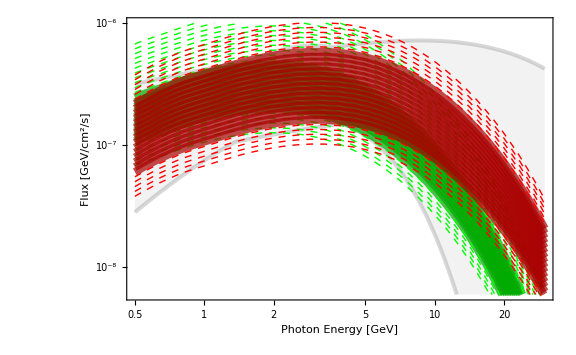

```mathematica
ftest=p2gam["b",40,#]&;
ftest2=p2gam["b",65,#]&;
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2},

func=ftest;
func2=ftest2;
numlines=25;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,maxE];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,maxE];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
x^2 func[x]#&/@goodnorms,
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@goodnorms2,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Good Curves: *)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2}},
FillingStyle->{Opacity[.1,Gray]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"},
ImageSize->Large(* or Large*)
]
]
```

#### Plotting two functions 2: prettier

```mathematica
SuperPlot[func_,norms_,MinEnv_,MaxEnv_,A_,numchecks_,minE_,maxE_]:=Module[
{goodnorms,badnorms},
goodnorms=GoodNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnv,MaxEnv,A,norms,numchecks,minE,maxE];

LogLogPlot[
Evaluate[Join[
x^2 func[x]#&/@goodnorms,
x^2 func[x]#&/@badnorms,

{MinEnv[x]/A,A MaxEnv[x]}]],
{x,minE,maxE},
PlotStyle->Join[
(* Good Curves: *)
Table[{Darker[Green]},{i,Length[goodnorms]}],
(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small]},{i,Length[badnorms]}],
(* Min/Max curves: *)
{{Black},{Black}}],
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Flux [GeV/cm^2/s]"}
(*PlotTheme->"Detailed"*)
]
]
```

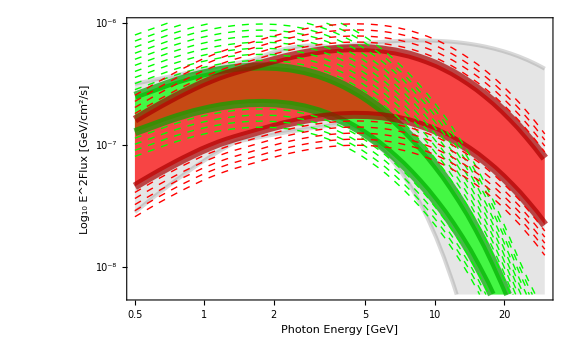

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/samplebbranges.png

```mathematica
ftest=p2gam["b",35,#]&;
ftest2=p2gam["b",100,#]&;
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=35;
m2=100;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,maxE];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,maxE];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
FrameTicks->{Automatic,expTicks,{},{}},
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.73,.75}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Green]],ImageScaled@{.73,.45}],

Text[Style["χχ̄→bb̄, a=2",18,Black],ImageScaled@{.25,.94}]
}
] 
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/samplebbranges.png",%]
```

### Comparing tc to bb

#### Some testing for candidate parameters

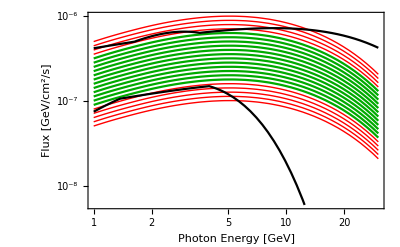

InterpolatingFunction::dmval: Input value {10^19\ Log[50]/20\ Log[10]} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {50} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

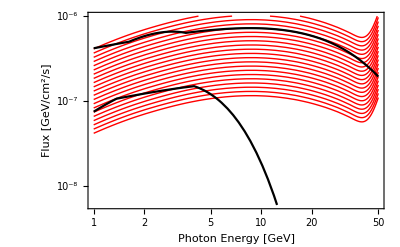

```mathematica
SuperPlot[
gettcfunc[dirtc,120],
RangeOfNorms[
gettcfunc[dirtc,120],
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
1, (* min E *)
30] (* max E *)

(*Check with maxE=50 to see how it fits*)

SuperPlot[
gettcfunc[dirtc,200],
RangeOfNorms[
gettcfunc[dirtc,200],
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
1, (* min E *)
50] (* max E *) (* just to demonstrate that this doesn't fit *)
```

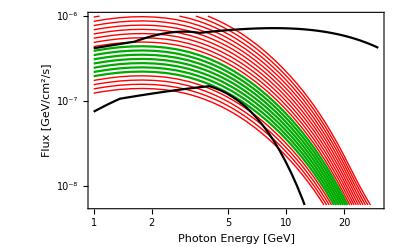

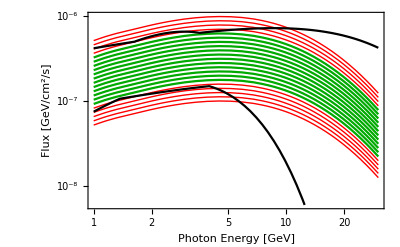

```mathematica
SuperPlot[
p2gam["b",35,#]&,
RangeOfNorms[
p2gam["b",35,#]&,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
1, (* min E *)
30] (* max E *)

SuperPlot[
p2gam["b",100,#]&,
RangeOfNorms[
p2gam["b",100,#]&,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
1, (* min E *)
30] (* max E *)
```

#### Megaplot

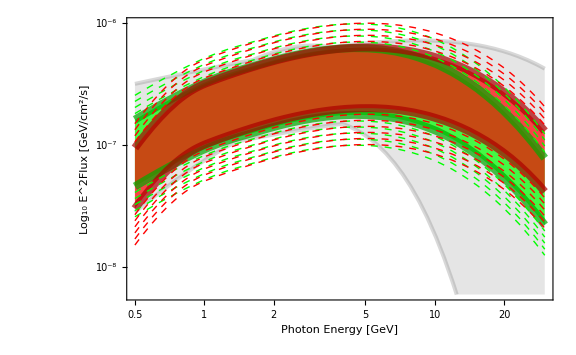

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/specbbvstc.png

```mathematica
ftest2=gettcfunc[dirtc,120];
ftest=p2gam["b",100,#]&;
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=100;
m2=120;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,maxE];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,maxE];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.73,.75}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Darker[Green]]],ImageScaled@{.73,.55}],

Text[Style["a=2",18,Gray],ImageScaled@{.18,.92}],

Text[Rotate[Style[
"χχ̄→bb̄"
,19,White,Background->Opacity[.7,Darker[Green]]],20Degree],ImageScaled@{.35,.60}],

Text[Rotate[Style[
"χχ̄→tc̄"
,19,White,Background->Opacity[.7,Darker[Red]]],20Degree],ImageScaled@{.35,.73}]

(*Text[Style["χχ̄→bb̄, a=2",18,Black],ImageScaled@{.3,.92}]*)
}
] 
]//Quiet

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/specbbvstc.png",%]
```

### Range of VV

#### Some tests

```mathematica
dirqq="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/VVtoqq/VV_q";
```

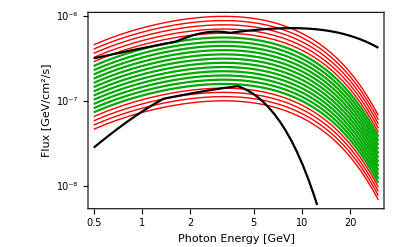

```mathematica
SuperPlot[
GetFunc[dirqq,{60,21}],
RangeOfNorms[
GetFunc[dirqq,{60,21}],
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
.5, (* min E *)
30] (* max E *)
```

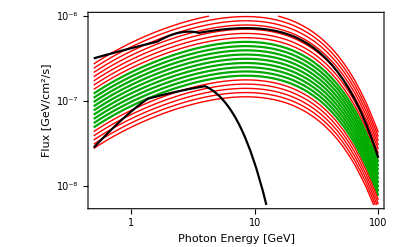

```mathematica
SuperPlot[
GetFunc[dirqq,{171,21}],
RangeOfNorms[
GetFunc[dirqq,{171,21}],
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
20],(* Number of divisions *)
MinEnv,MaxEnv,
2, (* Envelope Scaling *)
20, (* Number of energies to check *)
.5, (* min E *)
100]
```

#### Megaplot

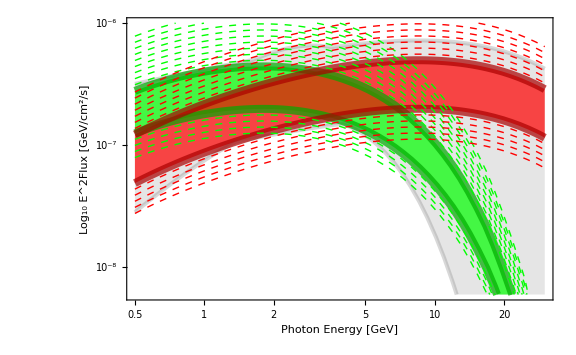

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrumVVs.png

```mathematica
ftest=GetFunc[dirqq,{33,21}];
ftest2=GetFunc[dirqq,{171,21}];
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=33;
m2=171;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.79,.78}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Darker[Green]]],ImageScaled@{.8,.5}],

Text[Style["χχ̄→VV (V→qq̄), a=2, m_V=21 GeV",18,Black],ImageScaled@{.35,.94}]
}
] 
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrumVVs.png",%]
```

#### Megaplot

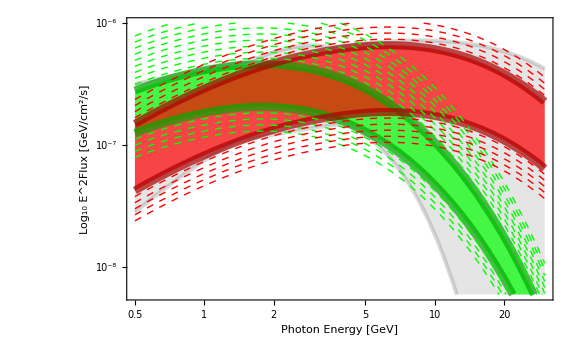

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrumVVbs.png

```mathematica
ftest=GetFunc[dirbb,{63,21}];
ftest2=GetFunc[dirbb,{249,21}];
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=63;
m2=249;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.77,.78}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Darker[Green]]],ImageScaled@{.8,.5}],

Text[Style["χχ̄→VV (V→bb̄), a=2, m_V=21 GeV",18,Black],ImageScaled@{.35,.94}]
}
] 
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrumVVbs.png",%]
```

### Phi Phi

```mathematica
dir3b="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/3ptobb/3p_b";
dir3q="/Users/fliptanedo/Documents/Work/PPPCMachineRunner/3ptoqq/3p_q";
```

#### bb

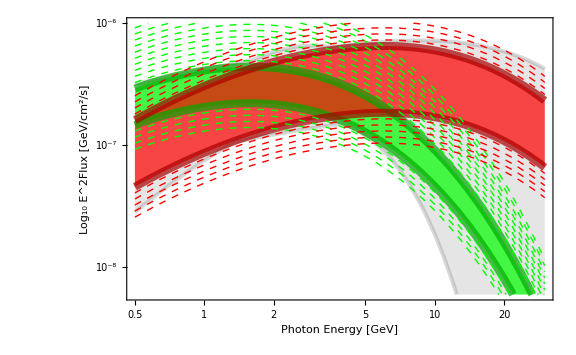

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrum3pbs.png

```mathematica
ftest=GetFunc[dir3b,{83,19}];
ftest2=GetFunc[dir3b,{343,19}];
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=83;
m2=343;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.77,.75}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Darker[Green]]],ImageScaled@{.8,.5}],

Text[Style["χχ̄→3φ (φ→bb̄), a=2, m_φ=19 GeV",18,Black],ImageScaled@{.35,.94}]
}
] 
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrum3pbs.png",%]
```

#### qq

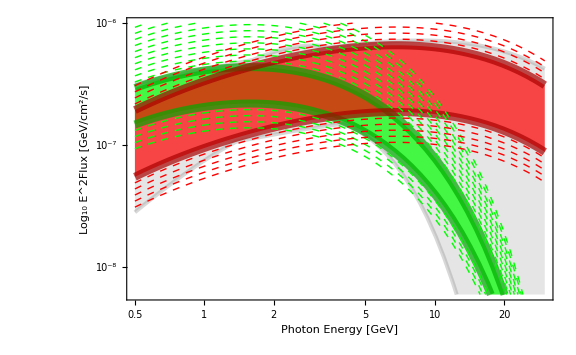

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrum3pqs.png

```mathematica
ftest=GetFunc[dir3q,{43,19}];
ftest2=GetFunc[dir3q,{195,19}];
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=43;
m2=195;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.76,.78}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Darker[Green]]],ImageScaled@{.8,.5}],

Text[Style["χχ̄→3φ (φ→qq̄), a=2, m_φ=19 GeV",18,Black],ImageScaled@{.35,.94}]
}
] 
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrum3pqs.png",%]
```

## Last tests

#### Megaplot

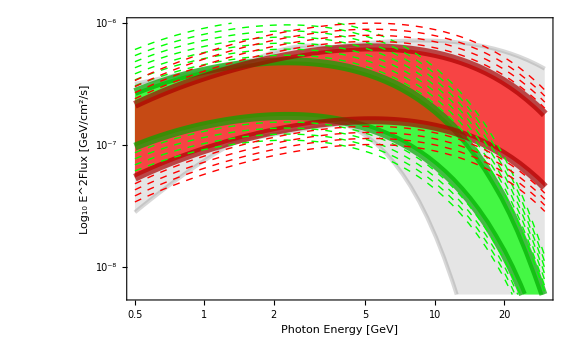

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrumVVsGoodMasses.png

```mathematica
m11=42;
m22=102;

ftest=GetFunc[dirqq,{m11,21}];
ftest2=GetFunc[dirqq,{m22,21}];
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=m11;
m2=m22;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.79,.78}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Darker[Green]]],ImageScaled@{.8,.5}],

Text[Style["χχ̄→VV (V→qq̄), a=2, m_V=21 GeV",18,Black],ImageScaled@{.35,.94}]
}
] 
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrumVVsGoodMasses.png",%]
```

#### bb

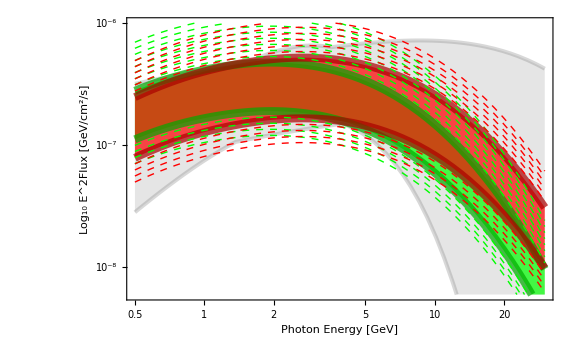

/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrum3pbsGoodMasses.png

```mathematica
m11=103;
m22=143;
ftest=GetFunc[dir3b,{m11,19}];
ftest2=GetFunc[dir3b,{m22,19}];
Module[
(*{func,norms,MinEnv,MaxEnv,A,numchecks,minE,maxE,goodnorms,badnorms}*)
{func,norms,goodnorms,badnorms,func2,norms2,goodnorms2,badnorms2,MinEnvF,MaxEnvF,A,numchecks,minE,maxE,envstyle,numlines,goodmin,goodmax,goodmin2,goodmax2,m1,m2,gsigmin,gsigmax,gsigmin2,gsigmax2},

func=ftest;
func2=ftest2;
numlines=20;
m1=m11;
m2=m22;
norm2sig1=(1/(4π 4)JFermi 1/m1^2 )^-1;
norm2sig2=(1/(4π 4)JFermi 1/m2^2 )^-1;

A=2;
MinEnvF=MinEnvR;
MaxEnvF=MaxEnv;
numchecks=20;
minE=.5;
maxE=30;
envstyle={(*Thick,*)Thickness[.005],Opacity[.3,Gray]};

norms =RangeOfNorms[
func,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

norms2 =RangeOfNorms[
func2,
MinEnv,MaxEnv,
3, (* Envelope Scaling *)
4, (* Test energy *)
numlines];

goodnorms=GoodNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
badnorms=BadNorms[func,MinEnvF,MaxEnvF,A,norms,numchecks,minE,maxE];
goodmin=goodnorms[[1]];
goodmax=goodnorms[[Length[goodnorms]]];
gsigmin=goodmin norm2sig1;
gsigmax=goodmax norm2sig1;

goodnorms2=GoodNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
badnorms2=BadNorms[func2,MinEnvF,MaxEnvF,A,norms2,numchecks,minE,100];
goodmin2=goodnorms2[[1]];
goodmax2=goodnorms2[[Length[goodnorms2]]];
gsigmin2=goodmin2 norm2sig2;
gsigmax2=goodmax2 norm2sig2;

LogLogPlot[
Evaluate[Join[
{MinEnvF[x]/A,A MaxEnvF[x]},
(*x^2 func[x]#&/@goodnorms,*)
{x^2 func[x]goodmin},
{x^2 func[x]goodmax},
(*x^2 func2[x]#&/@goodnorms2,*)
{x^2 func2[x]goodmin2},
{x^2 func2[x]goodmax2},
x^2 func[x]#&/@badnorms,
x^2 func2[x]#&/@badnorms2
]
],
{x,minE,maxE},

PlotStyle->Join[
(* Min/Max curves: *)
{{envstyle},{envstyle}},

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,Length[goodnorms]}],*)
Table[{Opacity[.7,Darker[Green]],Thickness[.01]},{i,2}],

(* Good Curves: *)
(*Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,Length[goodnorms2]}],*)
Table[{Opacity[.7,Darker[Red]],Thickness[.01]},{i,2}],

(* Bad Curves *)
Table[{Green,AbsoluteThickness[Small],Dashed},{i,Length[badnorms]}],

(* Bad Curves *)
Table[{Red,AbsoluteThickness[Small],Dashed},{i,Length[badnorms2]}]
],

Filling->{1->{2},3->{4},5->{6}},
FillingStyle->{
1->Directive[Opacity[0.2],Gray],
3->Directive[Opacity[0.7],Green],
5->Directive[Opacity[0.7],Red]},
PlotRange->{{minE,maxE},{MeVtoGeV 6 10^-6,MeVtoGeV 10^-3}},
BaseStyle->{FontFamily->"Helvetica",FontSize->18},
Frame->True,
GridLines->Automatic,
GridLinesStyle->{{Gray,Dotted},{Gray,Dotted}},
FrameTicks->{Automatic,expTicks,{},{}},
FrameLabel->{"Photon Energy [GeV]","Log_10 E^2Flux [GeV/cm^2/s]"},
ImageSize->Large,
Epilog->{
Text[Rotate[Style[
ToString[ScientificForm[gsigmin,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Green]],0Degree],ImageScaled@{.43,.32}],

Text[Rotate[Style[
ToString[ScientificForm[gsigmin2,2],TraditionalForm]<>" cm^3/s < ⟨σv⟩ < "<>ToString[ScientificForm[gsigmax2,2],TraditionalForm]<>" cm^3/s"
,19,Darker[Red]],0Degree],ImageScaled@{.43,.22}],

Text[Style["m_χ="<>ToString[m2]<>" GeV",18,White,Background->Opacity[.7,Red]],ImageScaled@{.77,.75}],

Text[Style["m_χ="<>ToString[m1]<>" GeV",18,White,Background->Opacity[.7,Darker[Green]]],ImageScaled@{.8,.5}],

Text[Style["χχ̄→3φ (φ→bb̄), a=2, m_φ=19 GeV",18,Black],ImageScaled@{.35,.94}]
}
] 
]

Export["/Users/fliptanedo/Dropbox/hooperonspectra/Mathematica/Machine/plots/spectrum3pbsGoodMasses.png",%]
```